#### Functions

```mathematica
Clear[makeLi]

makeLi[i_,parents_List,input_]:=Module[{num,den},If[i===input,
(*input node is left as a free variable*)
L[i],num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den]]

makeAllLi[g_Graph,input_]:=Association[Table[i->makeLi[i,VertexInComponent[g,i,{1}],input],{i,VertexList[g]}]]

expandLi[g_Graph,input_]:=Module[{defs,rules},defs=makeAllLi[g,input];
rules=Thread[L[#]->defs[#]&/@Keys[defs]];
FixedPoint[ReplaceAll[#,rules]&,defs]]


(*RandomDirectedGraphAdjacency[vertexCount_,edgeCount_]:=Module[{elems,adjacencyMatrix,graph},elems=RandomSample@PadRight[ConstantArray[1,edgeCount],vertexCount (vertexCount-1)/2];
adjacencyMatrix=Take[FoldList[RotateLeft,elems,Range[0,vertexCount-2]],All,vertexCount]~LowerTriangularize~-1;
adjacencyMatrix[[2,1]]=1;
adjacencyMatrix=Transpose[adjacencyMatrix];
graph=AdjacencyGraph[adjacencyMatrix]
(*<|"AdjacencyMatrix"->adjacencyMatrix,"Graph"->graph|>*)]*)

RandomDirectedGraphAdjacency[vertexCount_,edgeCount_,p_:0]:=Module[{elems,adjacencyMatrix,graph,backwardConnections,i,j},(*Original forward-only DAG construction*)elems=RandomSample@PadRight[ConstantArray[1,edgeCount],vertexCount (vertexCount-1)/2];
adjacencyMatrix=Take[FoldList[RotateLeft,elems,Range[0,vertexCount-2]],All,vertexCount]~LowerTriangularize~-1;
adjacencyMatrix[[2,1]]=1;
adjacencyMatrix=Transpose[adjacencyMatrix];
(*Add random backward connections with probability p*)If[p>0,
For[i=1,i<=vertexCount,i++,For[j=i+1,j<=vertexCount,j++,
(*Only add backward edge if there's no forward edge and random test passes*)
If[(*adjacencyMatrix[[i,j]]==0&&*)RandomReal[]<p,adjacencyMatrix[[j,i]]=1]]]];
graph=AdjacencyGraph[adjacencyMatrix]]


makeEquationSystem[g_Graph]:=Module[{nodes,eqns},nodes=VertexList[g];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];(*incoming neighbors*)
num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
L[i]==LT[i]*num/den],{i,nodes}];
eqns]

makeEquationSystemRHS[g_Graph]:=Module[{nodes,eqns},nodes=VertexList[g];
eqns=Table[Module[{parents,num,den},parents=VertexInComponent[g,i,{1}];(*incoming neighbors*)num=kf[i]+Total[Table[kf[i,p] L[p],{p,parents}]];
den=kt[i]+Total[Table[kt[i,p] L[p],{p,parents}]];
LT[i]*num/den-L[i]],{i,nodes}];
eqns]

RandomKFKTParams[g_Graph,input_,dist_:{-1,1}]:=Module[{nodes,otherNodes,rules},nodes=VertexList[g];
otherNodes=DeleteCases[nodes,input];
rules=Flatten@Table[Module[{nbrs=VertexInComponent[g,node],kfVal,krVal},
kfVal=Exp[RandomReal[dist]];
krVal=Exp[RandomReal[dist]];
Join[{
kf[node]->kfVal,
kt[node]->kfVal+krVal},
Table[Module[{
kfij=Exp[RandomReal[dist]],
krij=Exp[RandomReal[dist]]},
{kf[node,nbr]->kfij,
kt[node,nbr]->kfij+krij}],{nbr,nbrs}]//Flatten]],{node,otherNodes}];
rules]


RandomLTParams[g_Graph,input_,dist_:{-1,1}]:=Module[{nodes,otherNodes,rules},nodes=VertexList[g];
otherNodes=DeleteCases[nodes,input];
rules=Flatten@Table[LT[node]->Exp[RandomReal[dist]],{node,otherNodes}];
rules]

CreateFeedforwardNNGraph[nodesPerLayer_List]:=Module[
{layers,nodes,edges,graph,maxNodes,yCoords,nodePos, cumCounts,idx},

layers=Length[nodesPerLayer];
maxNodes=Max[nodesPerLayer];

(*Maximum number of nodes in any layer*)(*Create a list of nodes*)
(*nodes=Flatten[Table[Table[Subscript[v,i,j],{j,nodesPerLayer[[i]]}],{i,layers}]];
edges=Flatten[Table[DirectedEdge[Subscript[v,i,j],Subscript[v,i+1,k]],{i,layers-1},{j,nodesPerLayer[[i]]},{k,nodesPerLayer[[i+1]]}]];*)

(*Flattened node list as L[1],L[2],...*)
nodes=Table[i,{i,Total[nodesPerLayer]}];
cumCounts=Prepend[Most@Accumulate[nodesPerLayer],0];
idx[i_,j_]:=cumCounts[[i]]+j;
edges=Flatten[Table[DirectedEdge[idx[i,j],idx[i+1,k]],{i,layers-1},{j,nodesPerLayer[[i]]},{k,nodesPerLayer[[i+1]]}]];

(*Calculate y-coordinates to center nodes in each layer*)
yCoords=0.75*Table[Range[-(nodesPerLayer[[i]]-1)/2,(nodesPerLayer[[i]]-1)/2],{i,layers}];
(*Combine x and y coordinates for node positions*)
nodePos=Flatten[Table[Table[{0.5*i,yCoords[[i,j]]},{j,Length[yCoords[[i]]]}],{i,layers}],1];
(*Create the graph*)graph=Graph[nodes,edges,VertexStyle->Black,EdgeStyle->Directive[Black,Thickness[0.005]],VertexCoordinates->AssociationThread[nodes->nodePos],VertexSize->0.15,ImageSize->160];
graph]

upstream[node_]:=Select[nodes,
(*exclude the node itself*)
#!=node&&GraphDistance[g,#,node]<∞&];
downstream[node_]:=Select[nodes,
(*exclude the node itself*)
#!=node&&GraphDistance[g,node,#]<∞&];

convertToNumDenom[x_]:=NumeratorDenominator[Together[x]]
```

#### Scans

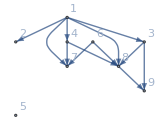

{-L[1]+(kf[1] LT[1])/kt[1],-L[2]+((kf[2]+kf[2,1] L[1]) LT[2])/(kt[2]+kt[2,1] L[1]),-L[3]+((kf[3]+kf[3,1] L[1]) LT[3])/(kt[3]+kt[3,1] L[1]),-L[4]+((kf[4]+kf[4,1] L[1]) LT[4])/(kt[4]+kt[4,1] L[1]),-L[5]+(kf[5] LT[5])/kt[5],-L[6]+(kf[6] LT[6])/kt[6],-L[7]+((kf[7]+kf[7,1] L[1]+kf[7,4] L[4]+kf[7,6] L[6]) LT[7])/(kt[7]+kt[7,1] L[1]+kt[7,4] L[4]+kt[7,6] L[6]),-L[8]+((kf[8]+kf[8,1] L[1]+kf[8,3] L[3]+kf[8,4] L[4]+kf[8,6] L[6]) LT[8])/(kt[8]+kt[8,1] L[1]+kt[8,3] L[3]+kt[8,4] L[4]+kt[8,6] L[6]),-L[9]+((kf[9]+kf[9,3] L[3]+kf[9,8] L[8]) LT[9])/(kt[9]+kt[9,3] L[3]+kt[9,8] L[8])}

```mathematica
(*layerList = {1,2,2,1};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList];*)

(*graph=Graph[{1->2,2->3,3->2(*,1->3*)},VertexLabels->"Name"];
nNodes = 3;*)

SeedRandom[30];
nNodes = 9;
nEdges = 12;
graph = RandomDirectedGraphAdjacency[nNodes,nEdges, 0.0];
(*coords=GraphEmbedding[graph];
graph = RandomDirectedGraphAdjacency[nNodes,nEdges, 0];*)

(*graph=RandomGraph[{nNodes,nEdges},DirectedEdges->True];*)

GraphPlot[graph,VertexLabels->Automatic]

eqs=makeEquationSystemRHS[graph]
```

```mathematica
eqs=makeEquationSystem[graph]
sol=Solve[eqs[[2;;nNodes]],Table[L[i],{i,2,nNodes}]]//Simplify;
(*L2expr=L[2]/.sol[[1]];
L3expr=L[3]/.sol[[1]];*)
expr = L[nNodes]/.sol[[1]];
allSimplePaths=FindPath[graph,1,nNodes,Infinity,All];
numberOfSimplePaths=Length[allSimplePaths]
(*num=D[L3expr,L[1]]//Simplify//Together//Numerator
Collect[num,L[1]]//TraditionalForm
CoefficientList[num,L[1]]//TraditionalForm*)
```

{L[1]==((kf[1]+kf[1,3] L[3]+kf[1,4] L[4]) LT[1])/(kt[1]+kt[1,3] L[3]+kt[1,4] L[4]),L[2]==((kf[2]+kf[2,1] L[1]+kf[2,3] L[3]) LT[2])/(kt[2]+kt[2,1] L[1]+kt[2,3] L[3]),L[3]==((kf[3]+kf[3,2] L[2]) LT[3])/(kt[3]+kt[3,2] L[2]),L[4]==((kf[4]+kf[4,2] L[2]+kf[4,3] L[3]) LT[4])/(kt[4]+kt[4,2] L[2]+kt[4,3] L[3])}

2

```mathematica
expr = expandLi[ graph,1][nNodes];
num = convertToNumDenom[expr][[1]];
num = convertToNumDenom[expr][[1]];
denom = convertToNumDenom[expr][[2]];
CoefficientList[num,L[1]]//Length
CoefficientList[denom,L[1]]//Length

allSimplePaths=FindPath[graph,1,nNodes,Infinity,All];
numberOfSimplePaths=Length[allSimplePaths]
```

2

2

1

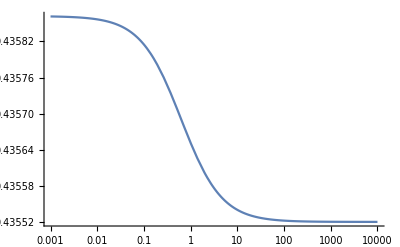

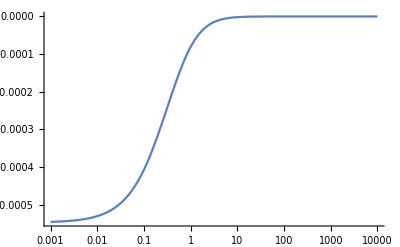

```mathematica
kfktRules=RandomKFKTParams[graph,1,{-1,4}];
ltRules=RandomLTParams[graph,1,{-1,4}];
allRules=Join[kfktRules,ltRules];

rhs = makeEquationSystemRHS[graph][[2;;]]/.allRules;

lower = 10^-3;
upper = 10^4;
L1Array = PowerRange[lower,upper,1.1];

(*LVars = Table[L[i],{i,1,nNodes}];
sols = Table[LVars[[2;;]]/.FindRoot[rhs/.L[1]->L1Array[[m]],Table[{LVars[[i]],LT[i]/.ltRules},{i,2,nNodes}],AccuracyGoal->10,PrecisionGoal->10],{m,1,Length[L1Array]}];
solFunc:=Interpolation[Transpose[{L1Array,sols[[;;,nNodes-1]]}]]*)

solFuncc[r_]:=Evaluate[expr/.allRules/.L[1]->r];
gradFunc = solFuncc';
LogLinearPlot[solFuncc[r],{r,lower,upper},PlotRange->Full]
LogLinearPlot[gradFunc[r],{r,lower,upper},PlotRange->Full]
```

```mathematica
(*layerList = {1,2,1};
nNodes = Total[layerList];
graph = CreateFeedforwardNNGraph[layerList]*)
SeedRandom[34];
expr = L[nNodes]/.sol[[1]];
lower = 10^-3;
upper = 10^3;
nPoints = 50;

L1Array = PowerRange[lower,upper,1.1];
samplePts=Table[10^r,{r,Log10[1.01lower],Log10[0.99upper],(Log10[upper]-Log10[lower])/nPoints}]//N;

signChangesList = {};

Do[

kfktRules=RandomKFKTParams[graph,1,{-1,4}];
     ltRules=RandomLTParams[graph,1,{-1,4}];
allRules=Join[kfktRules,ltRules];

(*rhs = makeEquationSystemRHS[graph][[2;;]]/.allRules;
LVars = Table[L[i],{i,1,nNodes}];
sols = Table[LVars[[2;;]]/.FindRoot[rhs/.L[1]->L1Array[[m]],Table[{LVars[[i]],LT[i]/.ltRules},{i,2,nNodes}],AccuracyGoal->10,PrecisionGoal->10,MaxIterations->5000,Method->{"Newton", "StepControl" -> "TrustRegion"}],{m,1,Length[L1Array]}];

solFunc:=Interpolation[Transpose[{L1Array,sols[[;;,nNodes-1]]}]];
gradFunc = solFunc';*)

     solFuncc[r_]:=Evaluate[expr/.allRules/.L[1]->r];
gradFunc=solFuncc';

  signChanges=Partition[samplePts,2,1]/. {a_,b_}:>If[Sign[gradFunc[a]]!=Sign[gradFunc[b]],{a,b},Nothing];

AppendTo[signChangesList,Length[signChanges]];
,{nIter,1,10000}
]//AbsoluteTiming
```

{85.0899,Null}

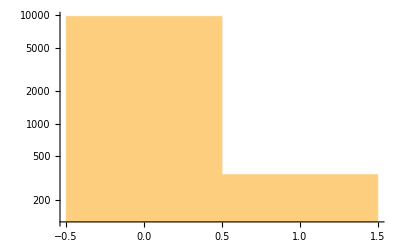

1

```mathematica
Histogram[signChangesList,ScalingFunctions->{None,"Log"}]
Max[signChangesList]
```

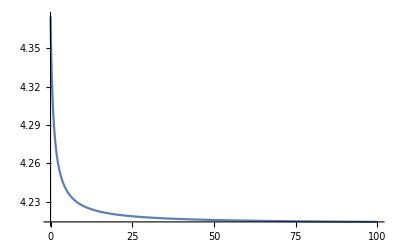

```mathematica
Plot[solFuncc[r],{r,0,100},PlotRange->Full]
```

```mathematica
Together[expr]
```

$Aborted

```mathematica
num
```

```mathematica
signChangesList
```

{0,0,0,0,0,0,0,0,0,0}